```mathematica
CrankNicolson[V_,ψ0_,L_,Ν_,T_,Δt_]:=
Block[{δ=L/(Ν-1.)},
Block[{H=SparseArray[{{n_,n_}->2./δ^2+V[-L/2+(n-1) δ],{n_,m_}/;Abs[n-m]==1->-1./δ^2},{Ν,Ν}],
ψ=Array[ψ0[-L/2+(#-1) δ]&,Ν]},
Block[{u=Inverse[IdentityMatrix[Ν]+I/2 Δt H].(IdentityMatrix[Ν]-I/2 Δt H)},
NestList[u.#&,ψ,T/Δt]
]
]
]
```

```mathematica
animate[V_,ψ0_,L_,Ν_,T_,Δt_]:=ListAnimate[ListPlot[#,PlotRange->{0,1},DataRange->{-L/2,L/2}]&/@(Abs[CrankNicolson[V,ψ0,L,Ν,T,Δt]]^2)]
norm[V_,ψ0_,L_,Ν_,T_,Δt_]:=ListPlot[Total[Abs[#]^2] L/Ν&/@CrankNicolson[V,ψ0,L,Ν,T,Δt]]
energy[V_,ψ0_,L_,Ν_,T_,Δt_]:=Block[{δ=L/(Ν-1.)},
Block[{H=SparseArray[{{n_,n_}->2./δ^2+V[-L/2+(n-1) δ],{n_,m_}/;Abs[n-m]==1->-1./δ^2},{Ν,Ν}]},
ListPlot[Abs[#.H.#]&/@CrankNicolson[V,ψ0,L,Ν,T,Δt]]
]
]
```

```mathematica
Timing[animate[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]]
```

{3.79688,}

```mathematica
Timing[CrankNicolson[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]][[1]]
```

0.109375

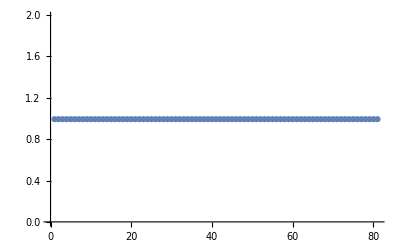

```mathematica
norm[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,150,1/2,1/160]
```

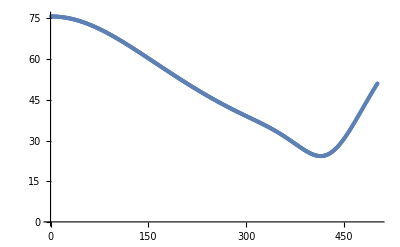

```mathematica
energy[0&,(Pi/2)^(-1/4) Exp[-#^2] Exp[I #]&,8,1000,1/2,1/1000]
```

```mathematica
animate[#^2&,1/(√8)(2 Pi)^(-1/4) Exp[-#^2/4] HermiteH[2,#/√2]&,12,150,1/2,1/160]
```